```mathematica
(* try rogers model *)
Clear[Qhat]
```

```mathematica
QQ=(1-u)((1-P)s+P Q);
```

```mathematica
Solve[QQ==Q,Q]
```

{{Q→((-1+P) s (-1+u))/(1-P+P u)}}

```mathematica
Qhat[P_]:=((-1+P) s (-1+u))/(1-P+P u);
```

```mathematica
W[p_,P_]:=w0+p Qhat[P]b+(1-p)(s b-c);
```

```mathematica
dWS=D[W[p,P],p]/.p->P
```

c-b s+(b (-1+P) s (-1+u))/(1-P+P u)

```mathematica
dWI=D[W[p,(1-P)],p]/.p->P
```

c-b s-(b P s (-1+u))/(P+(1-P) u)

```mathematica
Pstart=0.5;
imax=1000;
Ptab=Table[0,{i,imax}];
Ptab2=Table[0,{i,imax}];
dWStab=Table[0,{i,imax}];
dWItab=Table[0,{i,imax}];
delta=0.002;
sub={b->2,c->1,s->1,u->0.1};
Ptab[[1]]=Pstart;
Ptab2[[1]]=1-Pstart;
dWStab[[1]]=dWS/.sub/.{P->Pstart};
dWItab[[1]]=dWI/.sub/.{P->1-Pstart};
```

```mathematica
For[i=2,i<imax,i++,{
Ptab[[i]]=Ptab[[i-1]]+delta dWS/.sub/.{P->Ptab[[i-1]]};
Ptab[[i]]=If[Ptab[[i]]>1,1,Ptab[[i]]];
Ptab[[i]]=If[Ptab[[i]]<0,0,Ptab[[i]]];

Ptab2[[i]]=Ptab2[[i-1]]-delta dWI/.sub/.{P->Ptab2[[i-1]]};
Ptab2[[i]]=If[Ptab2[[i]]>1,1,Ptab2[[i]]];
Ptab2[[i]]=If[Ptab2[[i]]<0,0,Ptab2[[i]]];

dWStab[[i]]=dWS/.sub/.{P->Ptab[[i-1]]};
dWItab[[i]]=dWI/.sub/.{P->1-Ptab2[[i-1]]};
}];
```

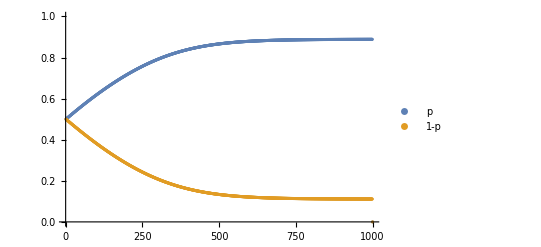

```mathematica
ListPlot[{Ptab,Ptab2},PlotRange->{All,{0,1}}, PlotLegends->{p,1-p}]
```

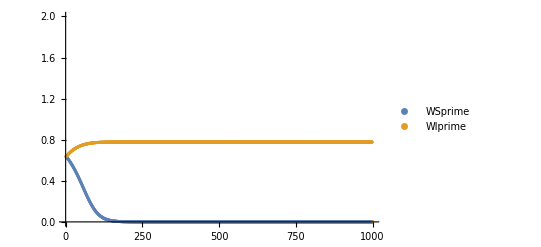

```mathematica
ListPlot[{dWStab,dWItab},PlotRange->{All,{0,2}}, PlotLegends->{WSprime,WIprime}]
```